```mathematica
filedata=Select[Import[FileNameJoin[{NotebookDirectory[],"Res\\out_pm0.2.csv"}],"Table","HeaderLines"->1,"FieldSeparators"->";"],Abs[#[[2]]]<0.8&];
filedata2=Import[FileNameJoin[{NotebookDirectory[],"Res\\out_85-90.csv"}],"Table","HeaderLines"->1,"FieldSeparators"->";"];
filedata3=Import[FileNameJoin[{NotebookDirectory[],"Res\\out_pm008.csv"}],"Table","HeaderLines"->1,"FieldSeparators"->";"];
filedata4=Import[FileNameJoin[{NotebookDirectory[],"Res\\out_m90.csv"}],"Table","HeaderLines"->1,"FieldSeparators"->";"];
```

```mathematica
liftdata=Join[filedata,filedata2,filedata3,filedata4][[All,{1,2,3,4}]];
```

```mathematica
liftdata2=Join[liftdata,Transpose@{liftdata[[;;,1]]*Cos[liftdata[[;;,2]]]},Transpose@{liftdata[[;;,1]]*Sin[liftdata[[;;,2]]]},2];
```

```mathematica
plotdata=liftdata2[[;;,{5,6,3,4}]];
```

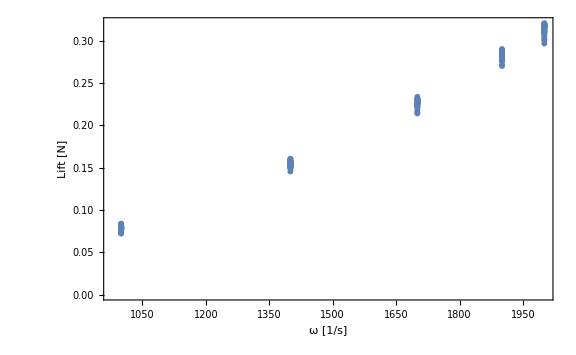

```mathematica
Show[ListPlot[{{#1,-#2}&@@@plotdata[[All,3;;4]]}],Frame->True,FrameLabel->{HoldForm[ω" [1/s]"],HoldForm["Lift [N]"]},LabelStyle-> {Black,FontSize->26,FontFamily->"Times"},PlotStyle->{{Blue,Thick},{Red,Thick}},ImageSize->Large]
```

FittedModel[0.000591722 vx^2-0.000025571 vx^4-0.000976456 vy-0.000138599 vx^2 vy+0.0000456088 vy^3-7.89381×10^-8 ω^2]

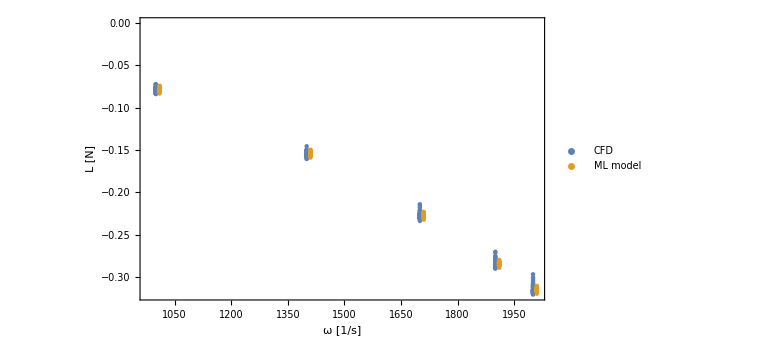

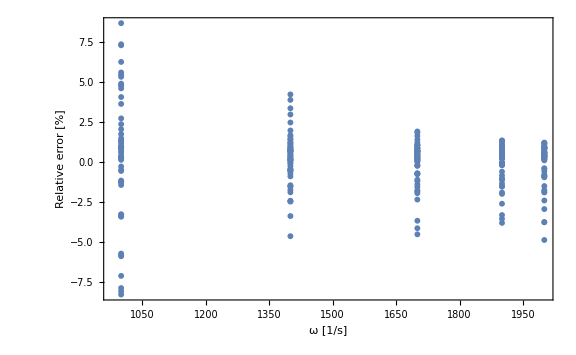

0.0782232

8.64921

```mathematica
SeedRandom[0];
training=RandomSample[plotdata,Floor[Length[plotdata]*0.9]];
plotdata2=plotdata;
model=LinearModelFit[training,{vy,vx^2 vy,ω^2,vx^2,vy^3,vx^4},{vx,vy,ω},IncludeConstantBasis->False]
Show[ListPlot[{plotdata[[All,3;;4]],Transpose[{Flatten[plotdata[[All,3]]+10],model@@@plotdata[[All,1;;3]]}]},PlotLegends->{"CFD","ML model"}],Frame->True,FrameLabel->{HoldForm[ω" [1/s]"],HoldForm[L"[N]"]},LabelStyle-> {Black,FontSize->26,FontFamily->"Times"},ImageSize->Large]
ListPlot[Transpose[{plotdata[[All,3]],(plotdata[[All,4]]-model@@@plotdata[[All,1;;3]])/plotdata[[All,4]]*100}],PlotRange->All,Frame->True,FrameLabel->{HoldForm[ω" [1/s]"],HoldForm["Relative error [%]"]},LabelStyle-> {Black,FontSize->26,FontFamily->"Times"},ImageSize->Large]
Mean[(plotdata[[All,4]]-model@@@plotdata[[All,1;;3]])/plotdata[[All,4]]*100]
Max[Abs[(plotdata[[All,4]]-model@@@plotdata[[All,1;;3]])/plotdata[[All,4]]*100]]
```

```mathematica
maxomega=Select[plotdata,#[[3]]==2000&];
```

```mathematica
magdata=Join[plotdata,Partition[√(plotdata[[All,1]]^2+plotdata[[All,2]]^2),1],2];
magdata[[All,4]]=-magdata[[All,4]];
ListPointPlot3D[{magdata[[All,{5,3,4}]],Partition[Flatten@Transpose@{magdata[[All,{5,3}]],-model@@@magdata[[All,1;;3]]},3]},PlotStyle->{Red,Blue},PlotLegends->{"CFD","ML model"},ImageSize->Large,AxesLabel->{HoldForm[v" [m/s]"],HoldForm[ω" [1/s]"],HoldForm["Lift [N]"]},LabelStyle-> {Black,FontSize->26,FontFamily->"Times"},ImagePadding->{{200,20},{20,20}}]
Show[ListPointPlot3D[Partition[Flatten@Transpose@{magdata[[All,{5,3}]],-model@@@magdata[[All,1;;3]]},3],PlotStyle->{Red,Blue},PlotLegends->{"CFD","ML model"},ImageSize->Large,AxesLabel->{HoldForm[v" [m/s]"],HoldForm[ω" [1/s]"],HoldForm["Lift [N]"]},LabelStyle-> {Black,FontSize->26,FontFamily->"Times"},ImagePadding->{{200,20},{20,20}}],ListPlot3D[magdata[[All,{5,3,4}]],PlotStyle->Red,InterpolationOrder->3]]
```

-Graphics3D-

-Graphics3D-

```mathematica
ListPlot3D[magdata[[All,{5,3,4}]],ImageSize->Large,InterpolationOrder->3,PlotStyle->{Opacity[0.3],Blue},AxesLabel->{HoldForm[v" [m/s]"],HoldForm[ω" [rad/s]"],HoldForm["Lift [N]"]},LabelStyle-> {Black,FontSize->26,FontFamily->"Times"},ImagePadding->{{150,150},{100,100}}]
ListPlot3D[Partition[Flatten@Transpose@{magdata[[All,{5,3}]],Abs[100*(magdata[[All,4]]+model@@@magdata[[All,1;;3]])/magdata[[All,4]]]},3],ImageSize->Full,InterpolationOrder->3,PlotStyle->{Opacity[0.3],Blue},AxesLabel->{HoldForm[v" [m/s]"],HoldForm[ω" [rad/s]"],HoldForm["Error [%]"]},LabelStyle-> {Black,FontSize->26,FontFamily->"Times"},ImagePadding->{{150,150},{100,100}},PlotRange->{All,All,{0,10}}]
```

-Graphics3D-

-Graphics3D-

FittedModel[7.63051×10^-8 ω^2]

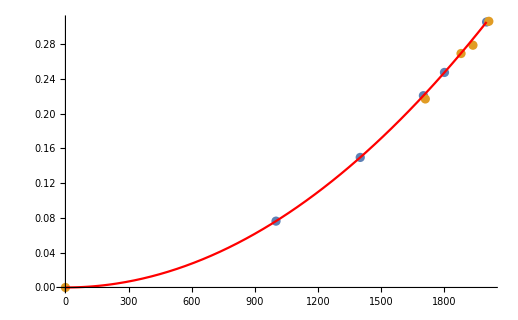

```mathematica
omegaModel=LinearModelFit[Transpose[{{1000,1400,1700,1800,2000},-{-0.07627891927495813,-0.1495261294140633,-0.2205163583523326,-0.2472323961025555,-0.305243511070259}}],{ω^2},ω,IncludeConstantBasis->False]
Show[ListPlot[{Transpose[{{1000,1400,1700,1800,2000},-{-0.07627891927495813,-0.1495261294140633,-0.2205163583523326,-0.2472323961025555,-0.305243511070259}}],{{0,0},{(16320 2 π)/60,0.867/4},{(17940 2 π)/60,1.076/4},{(18480 2 π)/60,1.1142/4},{(19200 2 π)/60,1.224/4}}}],Plot[omegaModel[ω],{ω,0,2000},PlotStyle->Red]]
```